```mathematica
Quit
```

Local process id:

```mathematica
$ProcessID
```

16024

#### Common Settings

Host and port:

```mathematica
host="18.217.160.48";
port="80";
```

#### GET

```mathematica
method="GET";
```

With GET:

```mathematica
EvaluationRequest[<|"Host"->host,"Port"->port,"Method"->method|>,{$ProcessID,$MachineName}]
```

{7705,ip-172-31-39-91}

```mathematica
ElapsedTime["ms",EvaluationRequest[<|"Host"->host,"Port"->port,"Method"->method|>,{$ProcessID,$MachineName}]]
```

162.005 ms

#### POST

```mathematica
method="POST";
```

With POST and BASE64:

```mathematica
EvaluationRequest[<|"Host"->host,"Port"->port,"Method"->method,"Encoding"->"Base64"|>,{$ProcessID,$MachineName}]
```

{7705,ip-172-31-39-91}

```mathematica
ElapsedTime["ms",EvaluationRequest[<|"Host"->host,"Port"->port,"Method"->method,"Encoding"->"Base64"|>,{$ProcessID,$MachineName}]]
```

240.325 ms

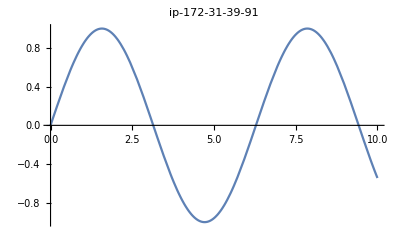

```mathematica
EvaluationRequest[<|"Host"->host,"Port"->port,"Method"->method,"Encoding"->"Base64"|>,Plot[Sin[x],{x,0,10},PlotLabel->$MachineName]]
```

```mathematica
ElapsedTime["ms",CloudEvaluate[Plot[Sin[x],{x,0,10},PlotLabel->$MachineName]]]
```

194.823 ms

```mathematica
ElapsedTime["ms",EvaluationRequest[<|"Host"->host,"Port"->port,"Method"->method,"Encoding"->"Base64"|>,Plot[Sin[x],{x,0,10},PlotLabel->$MachineName]]]
```

367.928 ms

```mathematica
Manipulate[
With[{a=a},
EvaluationRequest[<|"Host"->host,"Port"->port,"Method"->method,"Encoding"->"Base64"|>,Plot[Sin[a x],{x,0,10},PlotLabel->$MachineName,Filling->Axis]]],{a,1,10},ContinuousAction->False]
```